```mathematica
consttest={y->Pi/4,M->1,x->5};
consttest2={a->0.5};
simpconst={y->Pi/2,M->1}
rhor=(M+Sqrt[M^2-a^2])//.simpconst
supersimpconst={y->Pi/2,M->1,x->rhor}
hypersimpconst={y->Pi/2,M->1.0,a->0.0,x->rhor}
othersimpconst={y->Pi/2,M->1,a->1/2}
myassume={Im[M]==0,Im[a]==0,Im[x]==0,Im[y]==0}
```

{y→π/2,M→1}

1+√(1-a^2)

{y→π/2,M→1,x→1+√(1-a^2)}

{y→π/2,M→1.,a→0.,x→1+√(1-a^2)}

{y→π/2,M→1,a→1/2}

{Im[M]==0,Im[a]==0,Im[x]==0,Im[y]==0}

```mathematica
(* a=0 metric *)
mygcov={{-1+2/x,0,0,0},{0,x^2/(-2 x+x^2),0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[y]^2}}
es=Eigensystem[mygcov]
es[[1]]
es[[1]]//.consttest
Orthogonalize[es[[2]]]//.consttest

(* actual calculation *)
es=Eigensystem[mygcov];
FullSimplify[es[[1]]//.consttest//.consttest2];
es1new={es[[1,1]],es[[1,2]],es[[1,3]],es[[1,4]]};
es2new=Orthogonalize[{es[[2,1]],es[[2,2]],es[[2,3]],es[[2,4]]}];

(* Simplify some *)

es1new=Simplify[es1new//.{y->Pi/2,M->1},{Im[x]==0,x>rhor}];
es2new=Simplify[es2new//.{y->Pi/2,M->1},{Im[x]==0,x>rhor}];

mink=DiagonalMatrix[{-1,1,1,1}];
tetrcon=Table[es2new[[ii,jj]]/Sqrt[Abs[es1new[[ii]]]],{ii,1,4},{jj,1,4}];
tetrcov=Table[Sum[tetrcon[[jj,ll]]*mygcov[[ll,kk]]*mink[[pp,jj]],{jj,1,4},{ll,1,4}],{pp,1,4},{kk,1,4}];
MatrixForm[tetrcon];
MatrixForm[tetrcov];
```

{{-1+2/x,0,0,0},{0,x^2/(-2 x+x^2),0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[y]^2}}

{{(2-x)/x,x/(-2+x),x^2,x^2 Sin[y]^2},{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}}

{(2-x)/x,x/(-2+x),x^2,x^2 Sin[y]^2}

{-3/5,5/3,25,25/2}

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
utest={utest0,0,0,0}
Solve[utest.mygcov.utest==-1,utest0]
```

{utest0,0,0,0}

{{utest0→-1/(√((-2+x)/x))},{utest0→1/(√((-2+x)/x))}}

```mathematica
(* Get eigensystem and reorder so correctly ordered with original matrix *)
(*rhor=M+Sqrt[M^2-a^2]
x=p-rhor
*)
mygcov=FullSimplify[{{-1+(2 M x)/(x^2+a^2 Cos[y]^2),0,0,-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)},{0,(x^2+a^2 Cos[y]^2)/(a^2-2 M x+x^2),0,0},{0,0,x^2+a^2 Cos[y]^2,0},{-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2),0,0,(Sin[y]^2 ((a^2+x^2)^2-a^2 (a^2+x (-2 M+x)) Sin[y]^2))/(x^2+a^2 Cos[y]^2)}},{p>0,M>0}]//.othersimpconst
es=Eigensystem[mygcov];
es1new={es[[1,3]],es[[1,2]],es[[1,1]],es[[1,4]]};
es2new=Orthogonalize[{es[[2,3]],es[[2,2]],es[[2,1]],es[[2,4]]}];

(* Simplify some *)
es1new=Simplify[es1new//.simpconst,{Im[x]==0,Im[a]==0,x>=rhor}];
es2new=Simplify[es2new//.simpconst,{Im[x]==0,Im[a]==0,x>=rhor},TimeConstraint->1];

mink=DiagonalMatrix[{-1,1,1,1}];
tetrcon=Table[es2new[[ii,jj]]/Sqrt[Abs[es1new[[ii]]]],{ii,1,4},{jj,1,4}];
tetrcov=Table[Sum[tetrcon[[jj,ll]]*mygcov[[ll,kk]]*mink[[pp,jj]],{jj,1,4},{ll,1,4}],{pp,1,4},{kk,1,4}];
MatrixForm[tetrcon];
MatrixForm[tetrcov];
```

{{-1+2/x,0,0,-1/x},{0,x^2/(1/4-2 x+x^2),0,0},{0,0,x^2,0},{-1/x,0,0,(1/4 (-1/4-(-2+x) x)+(1/4+x^2)^2)/x^2}}

```mathematica
(* KS coords *)
mygcov=FullSimplify[{{-1+(2 M x)/(x^2+a^2 Cos[y]^2),(2 M x)/(x^2+a^2 Cos[y]^2),0,-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)},{(2 M x)/(x^2+a^2 Cos[y]^2),1+(2 M x)/(x^2+a^2 Cos[y]^2),0,-a (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2},{0,0,x^2+a^2 Cos[y]^2,0},{-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2),-a (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2,0,Sin[y]^2 (x^2+a^2 Cos[y]^2+a^2 (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2)}}//.othersimpconst]
es=Eigensystem[mygcov];
es1new={es[[1,4]],es[[1,3]],es[[1,1]],es[[1,2]]};
es2new=Orthogonalize[{es[[2,4]],es[[2,3]],es[[2,1]],es[[2,2]]}];

(* Simplify some *)
es1new=Simplify[es1new//.simpconst,{Im[x]==0,Im[a]==0,x>=rhor}];
(*es2new=Simplfy[es2new//.simpconst,{Im[x]==0,Im[a]==0,x>=rhor},TimeConstraint->1];*)

mink=DiagonalMatrix[{-1,1,1,1}];
tetrcon=Table[es2new[[ii,jj]]/Sqrt[Abs[es1new[[ii]]]],{ii,1,4},{jj,1,4}];
tetrcov=Table[Sum[tetrcon[[jj,ll]]*mygcov[[ll,kk]]*mink[[pp,jj]],{jj,1,4},{ll,1,4}],{pp,1,4},{kk,1,4}];
MatrixForm[tetrcon];
MatrixForm[tetrcov];
```

{{-1+2/x,2/x,0,-1/x},{2/x,(2+x)/x,0,-(2+x)/(2 x)},{0,0,x^2,0},{-1/x,-(2+x)/(2 x),0,1/4+1/(2 x)+x^2}}

```mathematica
(* ALL METRICS, test order of eigensystem with a=0 metric *)
```

```mathematica
es1new//.consttest//.consttest2

Limit[es2new[[1,1]]//.consttest,{a->0}]
Limit[es2new[[1,2]]//.consttest,{a->0}]
Limit[es2new[[1,3]]//.consttest,{a->0}]
Limit[es2new[[1,4]]//.consttest,{a->0}]

Limit[es2new[[2,1]]//.consttest,{a->0}]
Limit[es2new[[2,2]]//.consttest,{a->0}]
Limit[es2new[[2,3]]//.consttest,{a->0}]
Limit[es2new[[2,4]]//.consttest,{a->0}]

Limit[es2new[[3,1]]//.consttest,{a->0}]
Limit[es2new[[3,2]]//.consttest,{a->0}]
Limit[es2new[[3,3]]//.consttest,{a->0}]
Limit[es2new[[3,4]]//.consttest,{a->0}]

Limit[es2new[[4,1]]//.consttest,{a->0}]
Limit[es2new[[4,2]]//.consttest,{a->0}]
Limit[es2new[[4,3]]//.consttest,{a->0}]
Limit[es2new[[4,4]]//.consttest,{a->0}]
```

{1/40 (495-5 √10777),100/61,25,1/40 (495+5 √10777)}

{(519+5 √10777)/(√(64+(519+5 √10777)^2))}

{0}

{0}

{8/(√(64+(519+5 √10777)^2))}

{0}

{1}

{0}

{0}

{0}

«1 more identical outputs»

{1}

{0}

{-(8 √(10777/5 (269393+2595 √10777)))/(53885+519 √10777)^(3/2)}

{0}

{0}

{√(1/2+519/(10 √10777))}

```mathematica
utest={utest0,0,0,0};
Sum[utest[[ii]]*mygcov[[ii,jj]]*utest[[jj]],{ii,1,4},{jj,1,4}]
```

utest0^2 (-1+2/x)

```mathematica
(* Test conversion to orthonormal basis *)
utest={utest0,0,0,0};
whichpart=1;
myutest0=Solve[utest.mygcov.utest==-1,utest0][[whichpart,1,2]];
myutest=utest//.{utest0->myutest0};
myutestortho=Table[Sum[tetrcov[[j,k]]*myutest[[k]],{k,1,4}],{j,1,4}];
myutestortho//.{x->7.,M->1,y->Pi/2.,a->0.0000000001}
```

{-1.00028,0,0,0.0237247}

```mathematica
bu={bu0,bu1,bu2,bu3};
bd=mygcov.bu;
uu={uu0,uu1,uu2,uu3};
Bu={0,B1,B2,B3};
bu0=Bu.mygcov.uu;
bu1=(B1+uu1*bu0)/uu0;
bu2=(B2+uu2*bu0)/uu0;
bu3=(B3+uu3*bu0)/uu0;
Clear[wu0];
coordu={wu0,0,0,0};
wu0=Solve[coordu.mygcov.coordu==-1,wu0][[2,1,2]];
(*Clear[wu0]*)
coordd=mygcov.coordu;
ud=mygcov.uu;
```

```mathematica
(*
(* full boost into comoving frame *)
gam=-coordu.mygcov.uu;
Lambda1=Table[KroneckerDelta[ii,jj],{ii,1,4},{jj,1,4}];
Lambda2=Table[1/(gam+1)*(coordu[[ii]]*coordd[[jj]]+uu[[ii]]*ud[[jj]]-gam*(uu[[ii]]*coordd[[jj]]+coordu[[ii]]*ud[[jj]]))+(uu[[ii]]*coordd[[jj]]-coordu[[ii]]*ud[[jj]]),{ii,1,4},{jj,1,4}];
Lambdagen=Lambda1+Lambda2;
*)
```

```mathematica
(* full boost of comoving-type vector (u.v=0) into comoving frame *)
gam=-coordu.mygcov.uu;
Lambda1=Table[KroneckerDelta[ii,jj],{ii,1,4},{jj,1,4}];
Lambda2=Table[coordd[[jj]]*(coordu[[ii]]+uu[[ii]])/(gam+1),{ii,1,4},{jj,1,4}];
Lambdagen=Lambda1+Lambda2;
```

```mathematica
(* radial boost *)
(*
vr=uu1/uu0;
beta=Sqrt[-mygcov[[2,2]]/mygcov[[1,1]]]*vr;
gam=(1+mygcov[[2,2]]/mygcov[[1,1]]*vr^2)^(-1/2);
Lambdaradial={{gam,-Sqrt[-mygcov[[2,2]]/mygcov[[1,1]]]*gam*beta,0,0},{-Sqrt[-mygcov[[1,1]]/mygcov[[2,2]]]*gam*beta,gam,0,0},{0,0,1,0},{0,0,0,1}};
*)
```

```mathematica
pos={x->6,uu1->-0.2,uu2->.05,uu3->-.2,y->Pi/2,M->1,a->0.5};
```

```mathematica
(* pick root of u^t *)
udotu=Sum[uu[[ii]]*mygcov[[ii,jj]]*uu[[jj]],{ii,1,4},{jj,1,4}];
choose=2;
myuu0=Solve[udotu==-1,uu0][[choose,1,2]];
(*myuu0=FullSimplify[myuu0,{x≥2}];*)
myuu0//.pos
(*Clear[myuu0]*)
```

2.02651

```mathematica
(*myreplace={uu0->myuu0,uu2->0,uu3->0};*)
myreplace={uu0->myuu0,y->Pi/2,uu2->0,M->1};
```

```mathematica
(*Lambda=Lambdaradial;*)
Lambda0=Lambdagen//.myreplace;
(* Form boost+orthonormalization *)
Lambda=Table[Sum[tetrcon[[ii,jj]]*Lambda0[[jj,kk]],{jj,1,4}],{ii,1,4},{kk,1,4}];
(* Obtain inverse *)
(*iLambda=Inverse[Lambda];*)
```

3.125

```mathematica
Limit[FullSimplify[Det[Lambda0//.myreplace]//.pos]]
```

Limit::argr: Limit called with 1 argument; 2 arguments are expected.

Limit[-2.60209×10^-16]

```mathematica
boostu=Table[Sum[Lambda[[jj,ii]]*uu[[ii]],{ii,1,4}]//.myreplace,{jj,1,4}];
boostu[[1]]//.pos
boostu[[2]]//.pos
boostu[[3]]//.pos
boostu[[4]]//.pos
```

0.0232432

-0.0634833

0

-0.0128464

```mathematica
boostu.mink.boostu//.pos
boostu.mygcov.boostu//.pos
gam//.myreplace//.pos
```

-2.24742

-1.49779

1.58568

```mathematica
(*
boostudown=Table[Sum[iLambda[[ii,jj]]*ud[[ii]],{ii,1,4}]//.myreplace,{jj,1,4}];
boostudown[[1]]//.pos
boostudown[[2]]//.pos
boostudown[[3]]//.pos
boostudown[[4]]//.pos
*)
```

```mathematica
(*boostdelta=Table[Sum[(Lambda[[kk,ii]]*iLambda[[jj,qq]]*KroneckerDelta[ii,jj])//.myreplace,{ii,1,4},{jj,1,4}],{kk,1,4},{qq,1,4}];
MatrixForm[boostdelta//.pos]
*)
```

```mathematica
boostbu=Table[Sum[(Lambda[[kk,ii]]*bu[[ii]])//.myreplace,{ii,1,4}],{kk,1,4}];
(*boostbu=Simplify[boostbu,{x≥2,uu1<0,Im[uu3]==0,Im[uu1]==0,Im[B1]==0,Im[B3]==0,Im[B2]==0}];*)
```

```mathematica
(*boostbd=Table[Sum[(iLambda[[jj,qq]]*bd[[jj]])//.myreplace,{jj,1,4}],{qq,1,4}];*)
(*boostbd=Simplify[boostbd,{x≥2,uu1<0,Im[uu3]==0,Im[uu1]==0,Im[B1]==0,Im[B3]==0,Im[B2]==0}];*)
```

```mathematica
(*Tud=Table[magenthalpy*uu[[ii]]*ud[[jj]]-bu[[ii]]*bd[[jj]]+(p+bu.bd)*KroneckerDelta[ii,jj],{ii,1,4},{jj,1,4}];*)
```

```mathematica
(*
Tud=Table[-bu[[ii]]*bd[[jj]],{ii,1,4},{jj,1,4}];
boost=Table[Sum[Lambda[[kk,ii]]*iLambda[[jj,qq]]*Tud[[ii,jj]],{ii,1,4},{jj,1,4}],{kk,1,4},{qq,1,4}];
boost=Simplify[boost//.myreplace,{x≥2,Im[uu3]==0,Im[uu1]==0,Im[B1]==0,Im[B3]==0,Im[B2]==0}];
*)
```

$Aborted

```mathematica
(* boosted orthonormal r-\phi stress *)
boostorthorphi=-boostbu[[2]]*boostbu[[4]];
```

```mathematica
(* boosted orthonormal r-\phi stress *)
(*boostorthorphi=-boostbu[[2]]*boostbd[[4]]*Sqrt[mygcov[[2,2]]/mygcov[[4,4]]];*)
```

```mathematica
(*FullSimplify[Limit[boostorthorphi,{wu0->Infinity}],{uu1<0,myuu0≥1}]*)
```

```mathematica
(* check *)
```

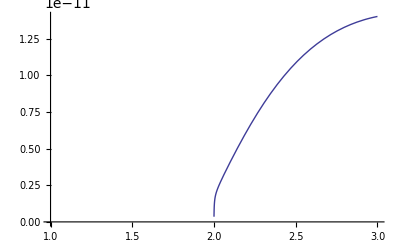

```mathematica
crapconst={a->1/2,y->Pi/2,B2->0,uu2->0,uu3->-0.818,uu1->-5.65,B1->-.000182,B3->-.00001};
value=boostorthorphi//.crapconst;
rhortoplot=rhor//.crapconst;
(*Plot[{-value/(2*Pi*x)},{x,0.95*rhortoplot,1.05*rhortoplot}]*)
Plot[{-value/(2*Pi*x)},{x,1,3}]
```

```mathematica
value//.{x->100}
```

-6.9408×10^-12

```mathematica
N[rhor//.othersimpconst]
```

1.86603

```mathematica
mygcov//.{x->2}
```

{{0,0,0,-1/2},{0,16,0,0},{0,0,4,0},{-1/2,0,0,9/2}}

```mathematica
myrhor=rhor//.othersimpconst
seriesboost=Series[boostorthorphi,{x,myrhor,0}];
```

1+(√3)/2

```mathematica
limitboost=Limit[seriesboost,{x->myrhor}]
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

```mathematica
FullSimplify[boostorthorphi//.crapconst]
```

-(4.47614×10^-6 (0.69753+wu0) (1.35945+wu0 (0.0159205+wu0)))/(1.+5.65 wu0)^2

```mathematica
(*Series[boostorthorphi,{x,2,1}];*)
```

```mathematica
(*final=Simplify[Normal[Series[boostorthorphi,{x,2,1}]]//.{y->Pi/2},{uu1<0},TimeConstraint->1];*)
```

Simplify::time: Time spent on a transformation exceeded 1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify :: "time" will be suppressed during this calculation.

```mathematica
(*Collect[final,B1]*)
```

```mathematica
(*Limit[final,{x->2}]*)
```

$Aborted

```mathematica
(*finalfinal=Simplify[final,{a≥0,uu1<0,x≥2},TimeConstraint->10];*)
```

Simplify::time: Time spent on a transformation exceeded 10 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify :: "time" will be suppressed during this calculation.

```mathematica
(*
rhor=1+Sqrt[1-a^2];
FullSimplify[finalfinal//.{x->rhor},{x>0,a>0,B1>0,uu1<0,B3<0,uu3>0}]
*)
```

```mathematica
(*
rhor=1+Sqrt[1-a^2];
Simplify[boostorthorphi//.{x->p-rhor,y->Pi/2},{p>=0,a>0,B1>0,uu1<0,B3<0,uu3>0},TimeConstraint->10]
*)
```

Simplify::time: Time spent on a transformation exceeded 10 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify :: "time" will be suppressed during this calculation.

$Aborted

```mathematica
rhor=1+Sqrt[1-a^2];
final=Simplify[boostorthorphi,{a>0,B1>0,B3<0,x≥rhor,uu1<0,uu3>0},TimeConstraint->3];
```

Simplify::time: Time spent on a transformation exceeded 3 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify :: "time" will be suppressed during this calculation.

$Aborted

```mathematica
boostorthorphi//.posnew//.{a->0.9,x->1.0000001*rhor}
```

-1.03586×10^-19+1.60876×10^-21 ⅈ

```mathematica
horfinal=Series[final,{x,rhor,0}];
```

```mathematica
Series[Normal[horfinal],{a,1/2,0}]
```

$Aborted

```mathematica
horfinal=Simplify[Series[final,{x,rhor,0}],{uu1<0,x>rhor}];
```

Hold[Abort[],Abort[]]

```mathematica
horfinala0=-((B1^2 uu3) (x-2)^(3/2))/(4 (√2 uu1))+O[x-2]^2
```

-((B1^2 uu3) (x-2)^(3/2))/(4 (√2 uu1))+O[x-2]^2

```mathematica
(* OTHER FAILED METHODS *)
```

```mathematica
rhor=1+Sqrt[1-a^2];
myassume={p>=0,a>0,B1>0,uu1<0,B3<0,uu3>0};
final=Normal[Series[boostorthorphi//.{y->Pi/2,x->rhor+p},{p,0,0}]];
```

-(((-2+x)/x)^(3/2) (B1 uu1 uu3 x+B3 (-2+x) (1+uu3^2 x^2+√((-2+x+uu1^2 x-2 uu3^2 x^2+uu3^2 x^3)/(-2+x)))) (B3 uu1 uu3 (-2+x) x^2+B1 (-2 (1+√((-2+x+uu1^2 x-2 uu3^2 x^2+uu3^2 x^3)/(-2+x)))+x (1+uu1^2+√((-2+x+uu1^2 x-2 uu3^2 x^2+uu3^2 x^3)/(-2+x))))))/((-2+x+uu1^2 x-2 uu3^2 x^2+uu3^2 x^3) (√((-2+x) x)+√(x (-2+x+uu1^2 x-2 uu3^2 x^2+uu3^2 x^3)))^2)

```mathematica
Limit[boostorthorphi,x->2]
```

$Aborted

```mathematica
posnew={uu1->-0.2,uu2->0.05,uu3->-0.2,y->π/2,M->1,B1->-.000182,B3->-.003389}
```

{uu1→-0.2,uu2→0.05,uu3→-0.2,y→π/2,M→1,B1→-0.000182,B3→-0.003389}

```mathematica
rhor=1+Sqrt[1-a^2];
boostorthorphi//.posnew//.{a->0.6,x->1.0001*rhor}
```

-6.58354×10^-16+4.35595×10^-15 ⅈ

```mathematica
rhor=1+Sqrt[1-a^2];
toplot=boostorthorphi//.posnew//.{x->p+rhor};
toplot//.{a->0.0001,p->0.000001}
(*ContourPlot[toplot,{a,0.00001,0.9},{p,0.00001,0.01}]*)
Plot3D[toplot,{a,0.00001,0.9},{p,0.00001,.1}]
```

ReplaceRepeated::reps: {posnew} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(-((0.+4.975×10^-7 ⅈ) (B1+uu1 (2.01005×10^6 B1 uu1+4. B3 uu3)))/(√(-1-2.01005×10^6 uu1^2-4. uu3^2))+(4.975×10^-7 uu1 (2.01005×10^6 B1 uu1+4. B3 uu3))/(1-(0.+1. ⅈ) √(-1-2.01005×10^6 uu1^2-4. uu3^2))) (((0.+0.000352668 ⅈ) (B3+uu3 (2.01005×10^6 B1 uu1+4. B3 uu3)))/(√(-1-2.01005×10^6 uu1^2-4. uu3^2))-(0.000352668 uu3 (2.01005×10^6 B1 uu1+4. B3 uu3))/(1-(0.+1. ⅈ) √(-1-2.01005×10^6 uu1^2-4. uu3^2)))//.posnew

ReplaceRepeated::reps: {posnew} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated :: "reps" will be suppressed during this calculation.

-Graphics3D-

```mathematica
toseries=boostorthorphi//.{x->p+rhor};
Series[toseries,{p,0,0}]
```

Hold[Abort[],Abort[]]

```mathematica
toseries=boostorthorphi//.{x->p+rhor,a->1/2};
Limit[toseries,{p->0},Analytic->True,Direction->-1,Assumptions->{a>0,uu1<0,B1>0,B3<0,uu3>0}]
```

$Aborted

```mathematica
toseries=boostorthorphi//.{x->p+rhor,a->0.0000000001};
toseries//.{p->0.00000001,uu1->-.3,uu3->0.1,B1->1,B3->-.5}
```

1190.34+0. ⅈ